### error-χ

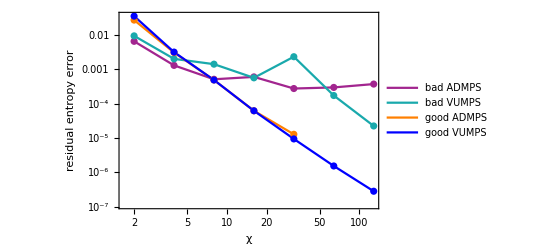

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};
bad VUMPS={{2,0.009417748318394648},{4,0.002015699144679528},{8,0.0014124333440985737},{16,0.0005648660818895084},{32,0.0023275213974344134},{64,0.00017254061460371688},{128,2.2398020855040623 10^-5}};
good VUMPS={{2,0.035383894448219266},{4,0.0031724461707100526},{8,0.0004885185976035156},{16,6.20736450483994 10^-5},{32,9.393607378116453 10^-6},{64,1.5324541302041972 10^-6},{128,2.8168339410994424 10^-7}};
bad ADMPS={{2,0.006535461228811464},{4,0.001301229298023176},{8,0.0005126369527924972},{16,0.0006014150393006847},{32,0.00027582932161660943},{64,0.0002969683615550182},{128,0.00037165789780096065}};
good ADMPS={{2,0.027157917703199926},{4,0.0030828688915959957},{8,0.0004888278749829391},{16,6.195331446570427 10^-5},{32,1.281415317687782 10^-5}};
ListLogLogPlot[{bad ADMPS,bad VUMPS,good ADMPS,good VUMPS},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"bad ADMPS","bad VUMPS","good ADMPS","good VUMPS"},{Scaled[{0.2,0.08}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{" residual entropy error",None},{HoldForm["χ"],None}},ImageSize->400]
```

### error-power iters

#### ising β_C

square ising  free energy error v.s. power iters  at  β_C=1/2 log(sqrt(2)+1)

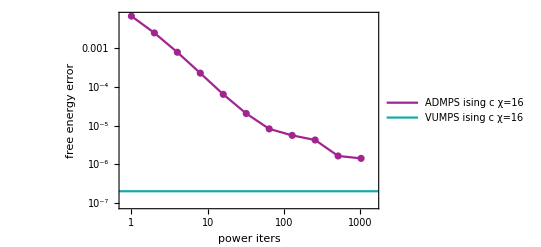

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};
ADMPS ising c=ToXY[{1,0.006707391051167194,
2,0.002472293122862504,
4,0.0007841945050308325,
8,0.00022633894867927744,
16,6.418281010933078 10^-5,
32,2.0567981247570683 10^-5,
64,8.256837729959756 10^-6,
128,5.601677110515338 10^-6,
256,4.260248255657433 10^-6,
512,1.649808288682375 10^-6,
1024,1.4294268085955894 10^-6
}];
VUMPS ising c={{10^-6,2.0285983703960397 10^-7},{2000,2.0285983703960397 10^-7}};
ListLogLogPlot[{ADMPS ising c,VUMPS ising c},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->{{0.8,1500},All},PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS ising c χ=16","VUMPS ising c χ=16"},{Scaled[{0.45,0.55}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"free energy error",None},{HoldForm["power iters"],None}},ImageSize->400]
```

#### ftol

Triangle ising  residual entropy  error v.s. iters , ftol is the AD optimization tolerance. Low tol means bad mps compression.

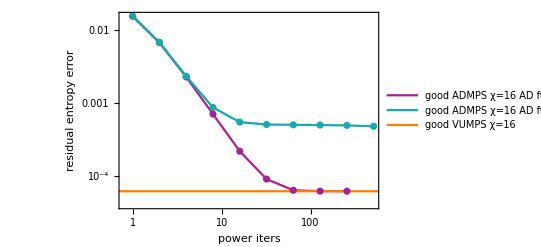

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};
good ADMPS 16 10={1,0.015734464219964373,
2,0.006810837646403181,
4,0.002297723342328781,
8,0.0007113183037121143,
16,0.0002198281625387441,
32,9.114831689143145 10^-5,
64,6.392172405528944 10^-5,
128,6.224338767179893 10^-5,
256,6.222610062844774 10^-5
};
good ADMPS 16 10 = Table[{good ADMPS 16 10[[i]],good ADMPS 16 10[[i+1]]},{i,1,Length[good ADMPS 16 10],2}];
good ADMPS 16 6={1,0.01574382955928763,
2,0.0068628142861601,
4,0.002352871065066581,
8,0.0008773975598295628,
16,0.0005519417899295388,
32,0.0005113443476376001,
64,0.0005067416223159993,
128,0.0005031197995867277,
256,0.0004972035416007918,
512,0.0004835959484085325
};
good ADMPS 16 6= Table[{good ADMPS 16 6[[i]],good ADMPS 16 6[[i+1]]},{i,1,Length[good ADMPS 16 6],2}];
good VUMPS={{10^-6,6.20736450483994 10^-5},{1000,6.20736450483994 10^-5}};
ListLogLogPlot[{good ADMPS 16 10,good ADMPS 16 6,good VUMPS},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->{{0.8,512},All},PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"good ADMPS χ=16 AD ftol=1e-10","good ADMPS χ=16 AD ftol=1e-6","good VUMPS χ=16"},{Scaled[{0.35,0.55}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"residual entropy error",None},{HoldForm["power iters"],None}},ImageSize->400]
```

#### χ

Good MPO power iters  exponential increase with designate error, which hints the good MPO is gapless.

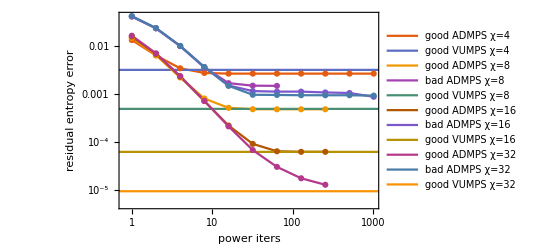

```mathematica
ToXY[data_]:=Table[{data[[i]],data[[i+1]]},{i,1,Length[data],2}];
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};
good ADMPS 4={1,0.01329238220974809,
2,0.006354057442743444,
4,0.0034170023991632226,
8,0.002736508587207857,
16,0.0026519089239456905,
32,0.0026505714641759186,
64,0.002650604430357717,
128,0.002650604699636301,
256,0.002650604699635801,
512,0.0026506046996358015,
1024,0.0026506046996364677
};
good ADMPS 4 =ToXY[good ADMPS 4];
good ADMPS 4={1,0.01329238220974809,
2,0.006354057442743444,
4,0.0034170023991632226,
8,0.002736508587207857,
16,0.0026519089239456905,
32,0.0026505714641759186,
64,0.002650604430357717,
128,0.002650604699636301,
256,0.002650604699635801,
512,0.0026506046996358015,
1024,0.0026506046996364677
};
good ADMPS 4 =ToXY[good ADMPS 4];
good ADMPS 8={1,0.01473381703807127,
2,0.006422957727969564,
4,0.002204579976862588,
8,0.0008013222416170755,
16,0.0005132629641312454,
32,0.00048063913039996,
64,0.0004790344701156693,
128,0.0004790265424002057,
256,0.000479026026425098
};
good ADMPS 8 =ToXY[good ADMPS 8];
good ADMPS 16=ToXY[{1,0.015734464219964373,
2,0.006810837646403181,
4,0.002297723342328781,
8,0.0007113183037121143,
16,0.0002198281625387441,
32,9.114831689143145 10^-5,
64,6.392172405528944 10^-5,
128,6.224338767179893 10^-5,
256,6.222610062844774 10^-5
}];
good ADMPS 32=ToXY[{1,0.016352333045601082,
2,0.007023838715291508,
4,0.002361907231407267,
8,0.0007140704388273571,
16,0.00021103114655279006,
32,6.760836247718696 10^-5,
64,3.0237010603488572 10^-5,
128,1.7488682098423543 10^-5,
256,1.281415317687782 10^-5
}];
bad ADMPS 8=ToXY[{1,0.04091987264645523,
2,0.023300263750682774,
4,0.009990375202270517,
8,0.003579044192452825,
16,0.0016796079987698395,
32,0.0014879225832610322,
64,0.0014743147316882042
}];
bad ADMPS 16=ToXY[{1,0.041599073805446314,
2,0.023425603098751722,
4,0.009946211580903024,
8,0.0035947022063958036,
16,0.0015016329690350483,
32,0.0011469150115763643,
64,0.001118277314230045,
128,0.001118044017758348,
256,0.001074236712022908,
512,0.0010469335028497435,
1024,0.0008720613869916198
}];
bad ADMPS 32=ToXY[{1,0.04183774559306625,
2,0.023552300351055978,
4,0.010000679169105707,
8,0.003642814702650279,
16,0.0014756314947476268,
32,0.0009609622242755188,
64,0.0009533374041296299,
128,0.0009410208960036645,
256,0.0009392669594142895,
512,0.0009393069041863062,
1024,0.0009227825050693829
}];
good VUMPS 4={{10^-6,0.0031724461707100526},{2000,0.0031724461707100526}};
good VUMPS 8={{10^-6,0.0004885185976035156},{2000,0.0004885185976035156}};
good VUMPS 16={{10^-6,6.20736450483994 10^-5},{2000,6.20736450483994 10^-5}};
good VUMPS 32={{10^-6,9.393607378116453 10^-6},{2000,9.393607378116453 10^-6}};
ListLogLogPlot[{good ADMPS 4,good VUMPS 4,good ADMPS 8,bad ADMPS 8,good VUMPS 8,good ADMPS 16,bad ADMPS 16,good VUMPS 16,good ADMPS 32,bad ADMPS 32,good VUMPS 32},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->{{0.8,1024},All},PlotLegends->{"good ADMPS χ=4","good VUMPS χ=4","good ADMPS χ=8","bad ADMPS χ=8","good VUMPS χ=8","good ADMPS χ=16","bad ADMPS χ=16","good VUMPS χ=16","good ADMPS χ=32","bad ADMPS χ=32","good VUMPS χ=32"},Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"residual entropy error",None},{HoldForm["power iters"],None}},ImageSize->400]
```